```mathematica
str="~nucleon";
list=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.txt","List"];
list2=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.2.txt","List"];
list3=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.3.txt","List"];
list4=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.4.txt","List"];
tflist0=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.tf - before.txt","List"];
tflist1=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.tf - alpha.txt","List"];
tflist2=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.tf - blue.txt","List"];
tflist3=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.tf - alpha - blue.txt","List"];
tflist4=Import[NotebookDirectory[]<>"..\\QtCuda\\"<>str<>".raw.tf - alpha - yellow.txt","List"];
intensity=Range[0,1,1/255];
```

```mathematica
PlotTF[intensity_,tflist_]:=Module[{colors,rgbfunction},
colors=RGBColor[ToExpression@#]&/@tflist[[All,1;;3]];
rgbfunction=Blend[Transpose@{intensity,colors},#]&;
ListLinePlot[Transpose@{intensity,tflist[[All,4]]},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,Filling->Axis,AxesLabel->{"Intensity","Alpha"},BaseStyle->{FontSize->14}]
]
```

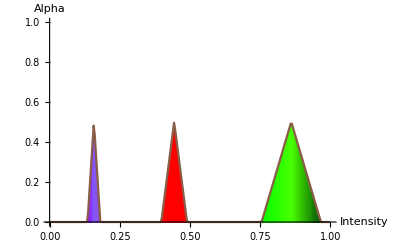

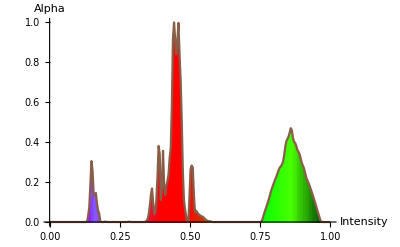

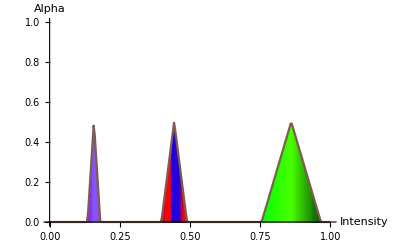

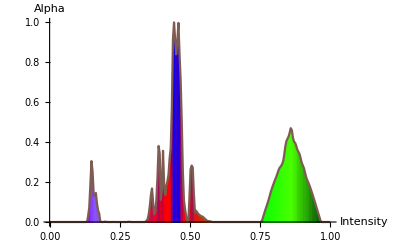

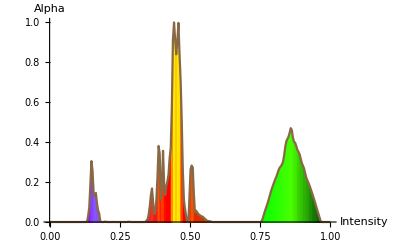

```mathematica
PlotTF[intensity,ToExpression/@tflist0]
PlotTF[intensity,ToExpression/@tflist1]
PlotTF[intensity,ToExpression/@tflist2]
PlotTF[intensity,ToExpression/@tflist3]
PlotTF[intensity,ToExpression/@tflist4]
```

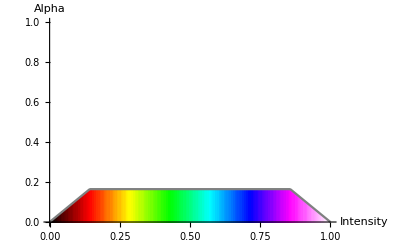

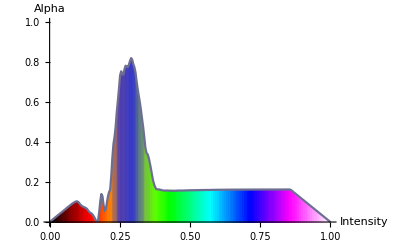

```mathematica
knee0=Import[NotebookDirectory[]<>"..\\cuda\\~CT-Knee.raw.tf - before.txt","List"];
knee1=Import[NotebookDirectory[]<>"..\\cuda\\~CT-Knee.raw.tf - after.txt","List"];
PlotTF[intensity,ToExpression/@knee0]
PlotTF[intensity,ToExpression/@knee1]
```

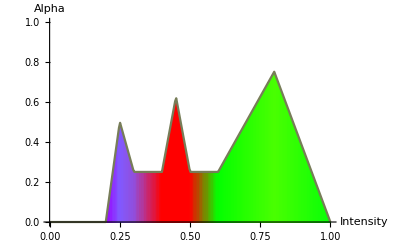

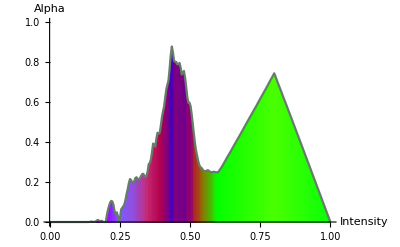

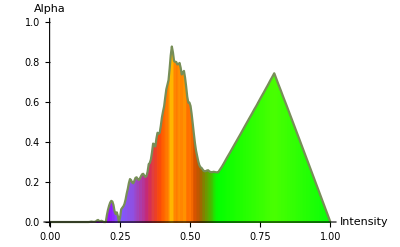

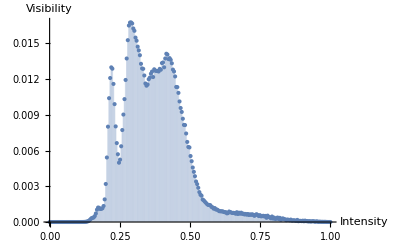

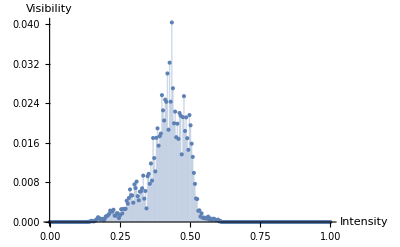

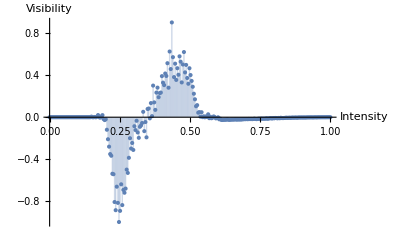

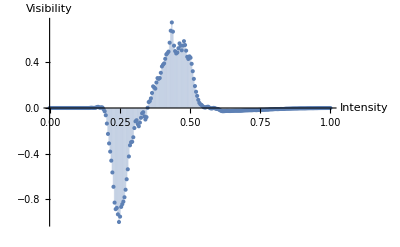

```mathematica
vorts=Import[NotebookDirectory[]<>"..\\cuda\\~vorts1.raw.txt","List"];
vorts2=Import[NotebookDirectory[]<>"..\\cuda\\~vorts1.raw.2.txt","List"];
vorts3=Import[NotebookDirectory[]<>"..\\cuda\\~vorts1.raw.3.txt","List"];
vorts4=Import[NotebookDirectory[]<>"..\\cuda\\~vorts1.raw.4.txt","List"];
vortex0=Import[NotebookDirectory[]<>"..\\cuda\\~vorts1.raw.tf - before.txt","List"];
vortex1=Import[NotebookDirectory[]<>"..\\cuda\\~vorts1.raw.tf - blue.txt","List"];
vortex2=Import[NotebookDirectory[]<>"..\\cuda\\~vorts1.raw.tf - yellow.txt","List"];
PlotTF[intensity,ToExpression/@vortex0]
PlotTF[intensity,ToExpression/@vortex1]
PlotTF[intensity,ToExpression/@vortex2]
ListPlot[vorts/Total@vorts//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[vorts2/Total@vorts2//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[vorts3//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[vorts4//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
```

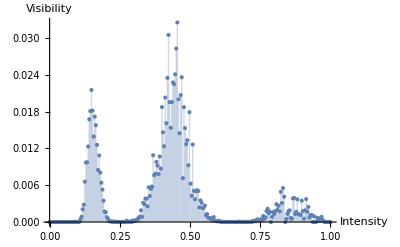

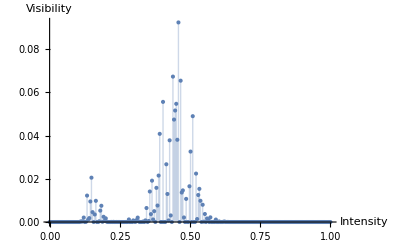

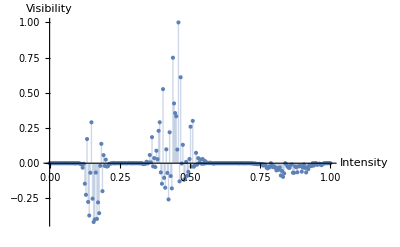

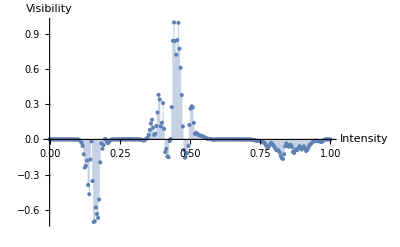

```mathematica
ListPlot[list/Total@list//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[list2/Total@list2//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[list3//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[list4//Transpose@{intensity,#}&,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
```

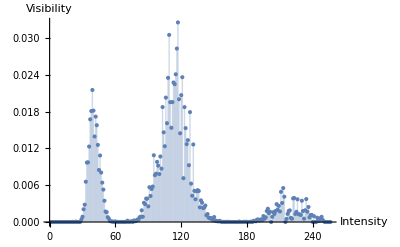

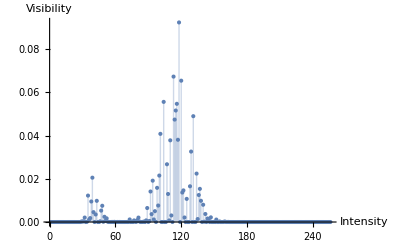

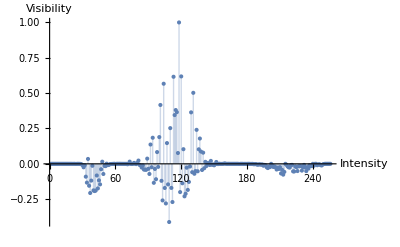

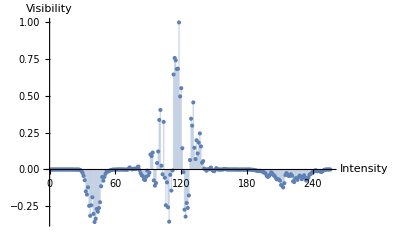

```mathematica
l3=list2/Total@list2-list/Total@list;
l4=GaussianFilter[l3,{7,1}];
ListPlot[list/Total@list,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[list2/Total@list2,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[l3/Max@Abs@l3,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
ListPlot[l4/Max@Abs@l4,PlotRange->All,AxesLabel->{"Intensity","Visibility"},BaseStyle->{FontSize->14},Filling->Axis]
```